NEWTON RAPHSON METHOD

```mathematica
Question 3.The equation f(x) is given as x^2-2x-1=0. Considering the initial guess at x=4 then the value of next approximation.Also plot graph.
```

```mathematica
x0 = Input["Enter initial guess : "];
Nmax = Input["Enter maximum number of iterations : "];
eps = Input["Enter a value of convergence parameter : "]; 
Print["x0=", x0]
```

x0=4

```mathematica
Print["Nmax=", Nmax]
```

Nmax=1

```mathematica
Print["epsilon=", eps]
```

epsilon=2

```mathematica
f[x] := x ^2 - 2 x - 1; 
Print["f(x) := ", f[x]]
```

f(x) := -1-2 x+x^2

```mathematica
Print["f'(x):= ", f'[x]]
```

f'(x):= -8+5 x^4

```mathematica
f[x_] := x ^2 - 2 x - 1;
Print["f'(x):= ", f'[x]]
```

f'(x):= -2+2 x

```mathematica
For[i = 1, i ≤ Nmax, i++, x1 = N[x0 - (f[x] /. x -> x0) / (f '[x] /. x -> x0)];
If[Abs[x1 - x0] < eps, Return[x1], x0p = x0; x0 = x1];
Print["In ", i , "th Number of iterations the approximation to root is : ", x1];
Print[" Estimated error is : ", Abs[x1 - x0]]]
```

Return[2.83333]

```mathematica
Print["the final approximation of root is : ", x1]
```

the final approximation of root is : 2.83333

```mathematica
Print[" Estimated error is : ", Abs[x1 - x0]]
```

Estimated error is : 1.16667

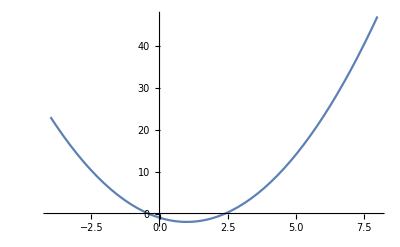

```mathematica
Plot[f[x], {x, -4, 8}]
```